```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
v2mColor=Purple;
```

```mathematica
(********************)
```

```mathematica
dateMouseSessionListV2m={{"030221","Mouse23310","Session1"},{"021721","Mouse23338","Session1"},{"030221","Mouse23338","Session1"},{"031621","Mouse23338","Session1"},{"031821","Mouse23338","Session2"},{"011721","Mouse23390","Session2"},{"011821","Mouse23390","Session2"},{"022821","Mouse23390","Session1"},{"021221","Mouse23359","Session2"},{"010321","Mouse23382","Session1"},{"010621","Mouse23382","Session2"}};
```

```mathematica
dateMouseSessionListV1toV2m={{"020421","Mouse23329","Session1"},{"021321","Mouse23329","Session1"},{"030121","Mouse23329","Session1"},{"030621","Mouse23329","Session1"},{"020421","Mouse23320","Session1"},{"121820","Mouse23365","Session1"},{"122020","Mouse23365","Session1"},{"062622","Mouse23007","Session1"}};
```

```mathematica
dateMouseSessionListLMtoV2m={{"092421","Mouse22422","Session1"},{"102221","Mouse22422","Session1"},{"101821","Mouse22436","Session1"},{"081621","Mouse22437","Session1"},{"081921","Mouse22437","Session1"},{"082821","Mouse22437","Session1"},{"102021","Mouse22472","Session1"},{"102821","Mouse22472","Session2"},{"082021","Mouse22491","Session1"},{"072022","Mouse23025","Session1"},{"071222","Mouse23100","Session1"},{"071522","Mouse23100","Session1"},{"070922","Mouse23014","Session1"},{"071422","Mouse23014","Session1"}};
```

```mathematica
dateMouseSessionListLPtoV2m={{"010721","Mouse23339","Session1"},{"010821","Mouse23339","Session1"},{"011421","Mouse23339","Session2"},{"011221","Mouse23369","Session1"},{"011521","Mouse23369","Session1"},{"121620","Mouse23381","Session2"},{"121920","Mouse23381","Session1"},{"120920","Mouse23384","Session1"},{"121320","Mouse23384","Session1"},{"063022","Mouse23067","Session1"},{"063022","Mouse23075","Session1"},{"071022","Mouse23075","Session1"}};
```

```mathematica
(********************)
```

```mathematica
(**********************************************)
(*******Generate plots in Figure 3H****************) 
(**********************************************)
```

```mathematica
meanDFFpupilPhaseV1toV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/V1toV2m/ValuesForPlotting/meanDFFpupilPhase_V1toV2m_nonDupROIs.txt","List"];
```

```mathematica
semDFFpupilPhaseV1toV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/V1toV2m/ValuesForPlotting/semDFFpupilPhase_V1toV2m_nonDupROIs.txt","List"];
```

```mathematica
meanDFFpupilPhaseLPtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LPtoV2m/ValuesForPlotting/meanDFFpupilPhase_LPtoV2m_nonDupROIs.txt","List"];
```

```mathematica
semDFFpupilPhaseLPtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LPtoV2m/ValuesForPlotting/semDFFpupilPhase_LPtoV2m_nonDupROIs.txt","List"];
```

```mathematica
meanDFFpupilPhaseLMtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LMtoV2m/ValuesForPlotting/meanDFFpupilPhase_LMtoV2m_nonDupROIs.txt","List"];
```

```mathematica
semDFFpupilPhaseLMtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LMtoV2m/ValuesForPlotting/semDFFpupilPhase_LMtoV2m_nonDupROIs.txt","List"];
```

```mathematica
meanDFFpupilPhaseV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/CellBodies/V2m/ValuesForPlotting/meanDFFpupilPhase_V2m.txt","List"];
```

```mathematica
semDFFpupilPhaseV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/CellBodies/V2m/ValuesForPlotting/semDFFpupilPhase_V2m.txt","List"];
```

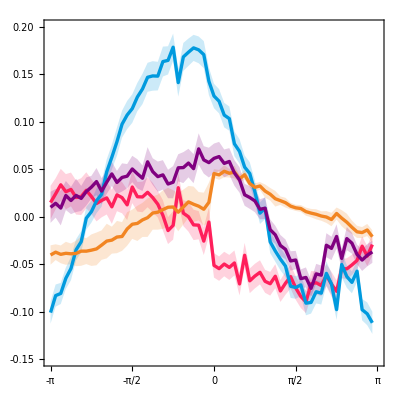

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFpupilPhaseV1toV2m,Part[#,2]&/@meanDFFpupilPhaseV1toV2m+(Part[#,2]&/@semDFFpupilPhaseV1toV2m),Part[#,2]&/@meanDFFpupilPhaseV1toV2m-(Part[#,2]&/@semDFFpupilPhaseV1toV2m),Part[#,2]&/@meanDFFpupilPhaseLPtoV2m,Part[#,2]&/@meanDFFpupilPhaseLPtoV2m+(Part[#,2]&/@semDFFpupilPhaseLPtoV2m),Part[#,2]&/@meanDFFpupilPhaseLPtoV2m-(Part[#,2]&/@semDFFpupilPhaseLPtoV2m),Part[#,2]&/@meanDFFpupilPhaseLMtoV2m,Part[#,2]&/@meanDFFpupilPhaseLMtoV2m+(Part[#,2]&/@semDFFpupilPhaseLMtoV2m),Part[#,2]&/@meanDFFpupilPhaseLMtoV2m-(Part[#,2]&/@semDFFpupilPhaseLMtoV2m),Part[#,2]&/@meanDFFpupilPhaseV2m,Part[#,2]&/@meanDFFpupilPhaseV2m+(Part[#,2]&/@semDFFpupilPhaseV2m),Part[#,2]&/@meanDFFpupilPhaseV2m-(Part[#,2]&/@semDFFpupilPhaseV2m)},Filling->{1->{{2},Directive[Opacity[0.2],v1Color]},1->{{3},Directive[Opacity[0.2],v1Color]},4->{{5},Directive[Opacity[0.2],lpColor]},4->{{6},Directive[Opacity[0.2],lpColor]},7->{{8},Directive[Opacity[0.2],lmColor]},7->{{9},Directive[Opacity[0.2],lmColor]},10->{{11},Directive[Opacity[0.2],v2mColor]},10->{{12},Directive[Opacity[0.2],v2mColor]}},PlotStyle->{{v1Color,Thickness[0.006]},Transparent,Transparent,{lpColor,Thickness[0.006]},Transparent,Transparent,{lmColor,Thickness[0.006]},Transparent,Transparent,{v2mColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-π,(31 π)/32},PlotRange->{{-π,π},{-0.15,0.20}},FrameTicks->{{LinTicks[-0.15,0.20,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-π,π,π/2,4,TickLabelFunction->(Rationalize[#/π]*π&),MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(**********************************************)
(*******Generate plots in Figure 3G****************) 
(**********************************************)
```

```mathematica
meanDFFpupilCCV1toV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/V1toV2m/ValuesForPlotting/meanDFFpupilCrossCorr_V1toV2m_nonDupROIs.txt","List"];
```

```mathematica
semDFFpupilCCV1toV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/V1toV2m/ValuesForPlotting/semDFFpupilCrossCorr_V1toV2m_nonDupROIs.txt","List"];
```

```mathematica
(*********)
```

```mathematica
meanDFFpupilCCLPtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LPtoV2m/ValuesForPlotting/meanDFFpupilCrossCorr_LPtoV2m_nonDupROIs.txt","List"];
```

```mathematica
semDFFpupilCCLPtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LPtoV2m/ValuesForPlotting/semDFFpupilCrossCorr_LPtoV2m_nonDupROIs.txt","List"];
```

```mathematica
(*********)
```

```mathematica
meanDFFpupilCCLMtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LMtoV2m/ValuesForPlotting/meanDFFpupilCrossCorr_LMtoV2m_nonDupROIs.txt","List"];
```

```mathematica
semDFFpupilCCLMtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LMtoV2m/ValuesForPlotting/semDFFpupilCrossCorr_LMtoV2m_nonDupROIs.txt","List"];
```

```mathematica
(*********)
```

```mathematica
meanDFFpupilCCV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/CellBodies/V2m/ValuesForPlotting/meanDFFpupilCrossCorr_V2m.txt","List"];
```

```mathematica
semDFFpupilCCV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/CellBodies/V2m/ValuesForPlotting/semDFFpupilCrossCorr_V2m.txt","List"];
```

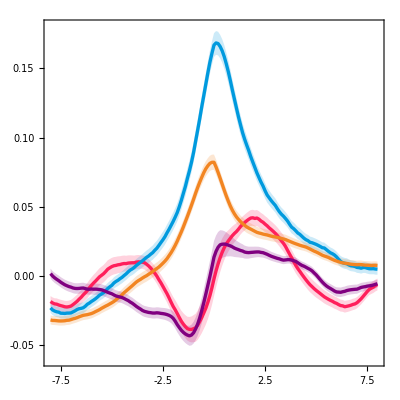

```mathematica
ListLinePlot[{Part[#,2]&/@meanDFFpupilCCV1toV2m,Part[#,2]&/@meanDFFpupilCCV1toV2m+(Part[#,2]&/@semDFFpupilCCV1toV2m),Part[#,2]&/@meanDFFpupilCCV1toV2m-(Part[#,2]&/@semDFFpupilCCV1toV2m),Part[#,2]&/@meanDFFpupilCCLPtoV2m,Part[#,2]&/@meanDFFpupilCCLPtoV2m+(Part[#,2]&/@semDFFpupilCCLPtoV2m),Part[#,2]&/@meanDFFpupilCCLPtoV2m-(Part[#,2]&/@semDFFpupilCCLPtoV2m),Part[#,2]&/@meanDFFpupilCCLMtoV2m,Part[#,2]&/@meanDFFpupilCCLMtoV2m+(Part[#,2]&/@semDFFpupilCCLMtoV2m),Part[#,2]&/@meanDFFpupilCCLMtoV2m-(Part[#,2]&/@semDFFpupilCCLMtoV2m),Part[#,2]&/@meanDFFpupilCCV2m,Part[#,2]&/@meanDFFpupilCCV2m+(Part[#,2]&/@semDFFpupilCCV2m),Part[#,2]&/@meanDFFpupilCCV2m-(Part[#,2]&/@semDFFpupilCCV2m)},Filling->{1->{{2},Directive[Opacity[0.2],v1Color]},1->{{3},Directive[Opacity[0.2],v1Color]},4->{{5},Directive[Opacity[0.2],lpColor]},4->{{6},Directive[Opacity[0.2],lpColor]},7->{{8},Directive[Opacity[0.2],lmColor]},7->{{9},Directive[Opacity[0.2],lmColor]},10->{{11},Directive[Opacity[0.2],v2mColor]},10->{{12},Directive[Opacity[0.2],v2mColor]}},PlotStyle->{{v1Color,Thickness[0.006]},Transparent,Transparent,{lpColor,Thickness[0.006]},Transparent,Transparent,{lmColor,Thickness[0.006]},Transparent,Transparent,{v2mColor,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.06,0.18}},FrameTicks->{{LinTicks[-0.06,0.18,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(***********************)
```

```mathematica
(**********************************************)
(*******Generate plots in Figure 3I****************) 
(**********************************************)
```

```mathematica
peakCCValsV1toV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/V1toV2m/ValuesForPlotting/peakDFFpupilCC_V1toV2m.txt","List"];
```

```mathematica
peakCCValsLPtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LPtoV2m/ValuesForPlotting/peakDFFpupilCC_LPtoV2m.txt","List"];
```

```mathematica
peakCCValsLMtoV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/Axons/LMtoV2m/ValuesForPlotting/peakDFFpupilCC_LMtoV2m.txt","List"];
```

```mathematica
peakCCValsV2m=ToExpression/@Import["F:/FigureGeneration/Figure3/Fig3Data/CellBodies/V2m/ValuesForPlotting/peakDFFpupilCC_V2m.txt","List"];
```

```mathematica
(**********************)
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[peakCCValsV1toV2m,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{All,{-0.07,0.65}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[peakCCValsV1toV2m,PlotRange->{All,{-0.07,0.65}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[-0.07,0.65,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[peakCCValsLMtoV2m,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{All,{-0.07,0.65}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[peakCCValsLMtoV2m,PlotRange->{All,{-0.07,0.65}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[-0.07,0.65,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[peakCCValsLPtoV2m,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{All,{-0.07,0.65}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[peakCCValsLPtoV2m,PlotRange->{All,{-0.07,0.65}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[-0.07,0.65,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
v2mAxonCharts=Show[BoxWhiskerChart[peakCCValsV2m,{{"Whiskers", Directive[Darker@v2mColor,Thick]}, {"Fences", Directive[Darker@v2mColor,Thick]},{"MedianMarker", Directive[Darker@v2mColor,Thickness[0.009]]}},PlotRange->{All,{-0.07,0.65}},ChartStyle->Directive[v2mColor,Opacity[0.3]],Frame->False],DistributionChart[peakCCValsV2m,PlotRange->{All,{-0.07,0.65}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v2mColor],Frame->False],FrameTicks->{{LinTicks[-0.07,0.65,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[peakCCValsV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{-0.07,0.65}},ChartStyle->Transparent,Frame->False],DistributionChart[peakCCValsV2m,PlotRange->{All,{-0.07,0.65}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[-0.07,0.65,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

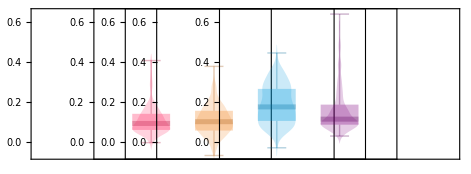

```mathematica
GraphicsRow[{v1AxonCharts,lmAxonCharts,lpAxonCharts,v2mAxonCharts,transp},Spacings->{{-280,-280,-280,-280,-480}}]
```